## Solution CP5: Complex numbers and matrices

This exercise demonstrates how Mathematica can be used to perform calculations with complex numbers, vectors and matrces.

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Complex numbers and functions

Notice that when dealing with complex numbers in Mathematica, √-1 is not denoted by i (as is standard in mathematics) but by the capital letter I, as it is standard to use capital letters for special numbers. Mathematica includes a number of commands to perform calculations with complex numbers, such as Re[] and Im[], that return respectively the real and imaginary part of a complex number. The commands Abs[] and Arg[] return the modulus and the argument, and the command AbsArg[] will convert a complex number z into polar coordinates (ω,ϕ) where ω is the radius Abs[z] and ϕ is the angle Arg[z] in the polar notation z=ω·(cos(ϕ)+sin(ϕ)·i). The command Conjugate[] calculates the complex conjugate. 
The commands ListPlot[] and ParametricPlot[] can be used to plot complex numbers and complex-valued functions, respectively. However, for all plotting purposes you need to enter the real and imaginary parts of complex numbers as separate variables. For examples, see chapter 7 of the Mathematica tutorial.

### Exercise 5-1

#### Complex numbers

Consider the following complex numbers: λ_1=1+i, λ_2= -2+1/2 i, λ_3= 1/2-2i.

(a) Plot λ_1, λ_2 and λ_3 in one graph

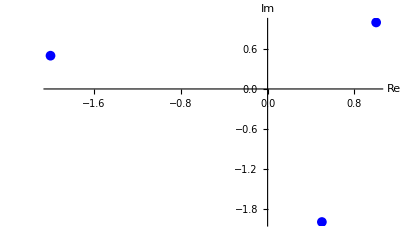

```mathematica
l1=1+I;
l2=-2+0.5I;
l3=0.5-2I;
z={l1, l2, l3};
ListPlot[Table[{Re[z[[k]]], Im[z[[k]]]}, {k, 1, Length[z]}],AxesLabel->{"Re","Im"}, PlotMarkers->{Automatic, 10}, PlotStyle->Blue]
```

(b) Calculate the complex conjugate of  λ_1, λ_2 and λ_3

```mathematica
Table[Conjugate[z[[k]]], {k, 1, Length[z]}]
```

{1-ⅈ,-2.-0.5 ⅈ,0.5+2. ⅈ}

(c) Calculate the the absolute value and the argument of λ_1, λ_2 and λ_3

```mathematica
Table[Abs[z[[k]]], {k, 1, Length[z]}]
Table[Sqrt[Re[z[[k]]]^2 + Im[z[[k]]]^2], {k, 1, Length[z]}]
Table[Arg[z[[k]]], {k, 1, Length[z]}]
Table[ArcTan[Im[z[[k]]]/Re[z[[k]]]], {k, 1, Length[z]}]
```

{√2,2.06155,2.06155}

{√2,2.06155,2.06155}

{π/4,2.89661,-1.32582}

{π/4,-0.244979,-1.32582}

(d) Convert  λ_1, λ_2 and λ_3 into polar coordinates

```mathematica
Table[AbsArg[z[[k]]], {k, 1, Length[z]}]
```

{{√2,π/4},{2.06155,2.89661},{2.06155,-1.32582}}

(e) Calculate  3λ_1, 2 λ_2 and -2 λ_3 using both the regular notation and the polar coordinates notation

```mathematica
3*l1
AbsArg[3*l1]
2*l2
AbsArg[2*l2]
-2*l3
AbsArg[-2*l3]
```

3+3 ⅈ

{3 √2,π/4}

-4.+1. ⅈ

{4.12311,2.89661}

-1.+4. ⅈ

{4.12311,1.81577}

We can see that, mutiplying  a complex number by a scalar only change its length Abs[], but not its argument Arg[]

(f) Calculate λ_1+λ_3, 2 λ_1+λ_2 and 4 λ_2+λ_3

```mathematica
l1+l3
2l1+l2
4l2+l3
```

1.5-1. ⅈ

0.+2.5 ⅈ

-7.5+0. ⅈ

(g) Calculate λ_1·λ_2, λ_1·λ_3 and λ_2·λ_3 using either the regular notation or the polar coordinates notation

```mathematica
l1*l2
AbsArg[l1*l2]
l1*l3
AbsArg[l1*l3]
l2*l3
AbsArg[l2*l3]
```

-2.5-1.5 ⅈ

{2.91548,-2.60117}

2.5-1.5 ⅈ

{2.91548,-0.54042}

0.+4.25 ⅈ

{4.25,1.5708}

(h) Calculate  λ_1^4, λ_2^4 and λ_3^4

```mathematica
l1^4
AbsArg[l1^4]
l2^4
AbsArg[l2^4]
l3^4
AbsArg[l3^4]
```

-4

{4,π}

10.0625-15. ⅈ

{18.0625,-0.979915}

10.0625+15. ⅈ

{18.0625,0.979915}

(i) Calculate 1/λ_1, 1/λ_2 and 1/λ_3

```mathematica
1/l1
1/l2
1/l3
```

1/2-ⅈ/2

-0.470588-0.117647 ⅈ

0.117647+0.470588 ⅈ

(j) Calculate λ_1/λ_2, λ_1/λ_3 and λ_2/λ_3 using either the regular notation or the polar coordinates notation

```mathematica
l1/l2
l1/l3
l2/l3
```

-0.352941-0.588235 ⅈ

-0.352941+0.588235 ⅈ

-0.470588-0.882353 ⅈ

(j) Calculate e^iπ , e^(iπ/2) and e^(iπ/4) , and plot them in one graph

```mathematica
Clear[z]
```

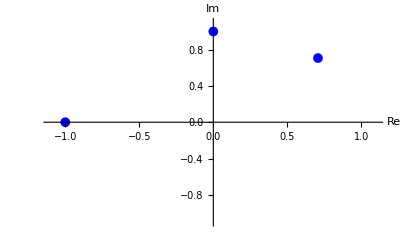

```mathematica
z={Exp[I*Pi], Exp[I*(Pi/2)], Exp[I*(Pi/4)]};
ListPlot[Table[{Re[z[[k]]], Im[z[[k]]]},{k, 1, Length[z]}], PlotRange->{{-1.1, 1.1}, {-1.1, 1.1}},AxesLabel->{"Re", "Im"}, PlotMarkers->{Automatic, 10}, PlotStyle->Blue]
```

#### Complex functions

Consider the function: e^((a+bi)t). Plot this function for the following value pairs (a,b). Hint: implement the function in polar coordinates notation.

(a) a=0.5, b=2π

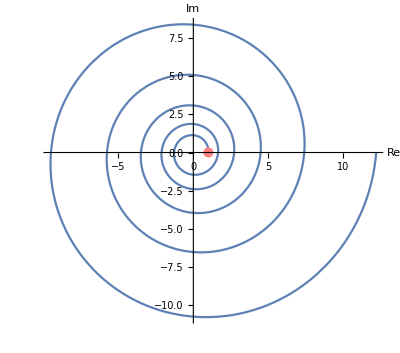

```mathematica
f[a_, b_]:=Exp[a*t]*(Cos[b*t]+I*Sin[b*t])
z=f[0.5, 2Pi];
init=z/.t->0;
spiral=ParametricPlot[{Re[z],Im[z]},{t,0,5}, AxesLabel->{"Re", "Im"}];
initPoint=ListPlot[{{Re[init], Im[init]}}, PlotMarkers->{Automatic, Medium}, PlotStyle->Pink];
Show[spiral, initPoint]
```

(b) a=-0.5, b=2π

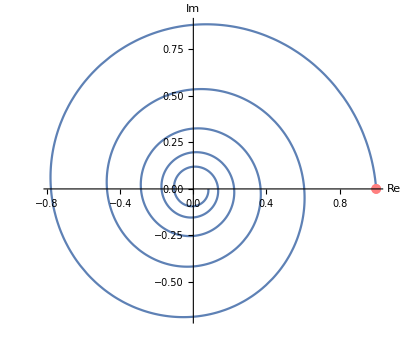

```mathematica
z=f[-0.5, 2Pi];
init=z/.t->0;
spiral=ParametricPlot[{Re[z],Im[z]},{t,0,5}, AxesLabel->{"Re", "Im"}];
initPoint=ListPlot[{{Re[init], Im[init]}}, PlotMarkers->{Automatic, Medium}, PlotStyle->Pink];
Show[spiral, initPoint]
```

(c) a=0.5, b=-2π

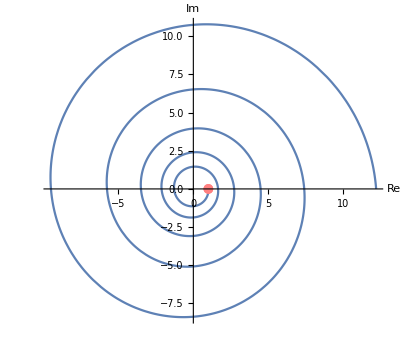

```mathematica
z=f[0.5, -2Pi];
init=z/.t->0;
spiral=ParametricPlot[{Re[z],Im[z]},{t,0,5}, AxesLabel->{"Re", "Im"}];
initPoint=ListPlot[{{Re[init], Im[init]}}, PlotMarkers->{Automatic, Medium}, PlotStyle->Pink];
Show[spiral, initPoint]
```

(d) a=0.1, b=10

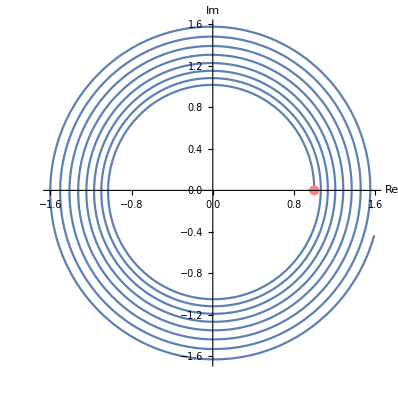

```mathematica
z=f[0.1, 10];
init=z/.t->0;
spiral=ParametricPlot[{Re[z],Im[z]},{t,0,5}, AxesLabel->{"Re", "Im"}];
initPoint=ListPlot[{{Re[init], Im[init]}}, PlotMarkers->{Automatic, Medium}, PlotStyle->Pink];
Show[spiral, initPoint]
```

## Matrices and vectors

In Mathematica vectors and matrices are represented as lists and nested lists (i.e., a list of lists), respectively. A matrix can be defined using the commands Table[] or Array[]; for examples, see chapter 8 of the Mathematica tutorial. The command MatrixForm[] is used to represent a list as a column vector or as a matrix in matrix notation. Mathematica knows a number of build-in commands to calculate characteristics of a matrix A, such as the trace Tr[A], the determinant Det[A], and the eigenvalues Eigenvalues[A]. The command CharacteristicPolynomial[A,λ] will calculate the characteristic equation of the matrix A for variable λ.

### Exercise 5-2: Multiplying matrices and vectors

Consider the matrices A=(1 | 0
-2 | 1
4 | 3) and B=(2 | 1
1 | -2) from the pen and paper practical.

(a) Calculate the product of A and the first column vector of B

```mathematica
matA={{1, 0}, {-2, 1}, {4, 3}};
MatrixForm[matA]
matB={{2, 1}, {1, -2}};
MatrixForm[matB]
```

(1 | 0
-2 | 1
4 | 3)

(2 | 1
1 | -2)

```mathematica
matA . matB[[All, 1]] // MatrixForm
```

(2
-3
11)

(b) Calculate the product of A and the second column vector of B

```mathematica
matA . matB[[All, 2]] // MatrixForm
```

(1
-4
-2)

(c) Calculate the matrix product AB

```mathematica
matA . matB // MatrixForm
```

(2 | 1
-3 | -4
11 | -2)

(d) Calculate the matrix product BA

```mathematica
matB . matA // MatrixForm
```

Dot::dotsh: Tensors {{2,1},{1,-2}} and {{1,0},{-2,1},{4,3}} have incompatible shapes.

{{2,1},{1,-2}}.{{1,0},{-2,1},{4,3}}

### Exercise 5-3: 2x2 matrices

Consider the matrices A1=(3 | 2
3 | -2), A2=(2 | -3
3 | 2) and A3=(4 | 2
-4 | -2) from the pen and paper practical.

(a) Calculate the sum of A1, A2 and A3

```mathematica
mA1={{3,2}, {3, -2}}; mA2={{2,-3}, {3, 2}}; mA3={{4, 2},{-4, -2}};
mA1+mA2 + mA3 // MatrixForm
```

(9 | 1
2 | -2)

(b) Calculate the product of A1, A2 and A3

```mathematica
mA1 . mA2 . mA3 // MatrixForm
```

(68 | 34
52 | 26)

(c) Calculate the trace, determinant and eigenvalues of A1, A2 and A3

```mathematica
Tr[mA1]
Det[mA1]
Eigenvalues[mA1]
```

1

-12

{4,-3}

### Exercise 5-4: 3x3 matrices

Consider the matrices B1=(1 | 0 | 0
2 | 2 | 0
-4 | 3 | 2), B2=(1 | 0 | 0
2 | 2 | -3
-4 | 3 | 2) and B3=(1 | 3 | -3
2 | 2 | -3
-4 | 3 | -2). 
Calculate the trace, determinant and eigenvalues of B1, B2 and B3. Check that the trace equals the sum of the eigenvalues and the determinant equals the product of the eigenvalues.

```mathematica
mB1={{1, 0,0}, {2,2,0}, {-4,3,2}};
tB1=Tr[mB1]
dB1=Det[mB1]
eB1=Eigenvalues[mB1]
Sum[eB1[[i]],{i, 1, Length[eB1]}]
Product[eB1[[i]],{i, 1, Length[eB1]}]
```

5

4

{2,2,1}

5

4

```mathematica
mB2={{1,0,0}, {2,2,-3}, {-4, 3, 2}};
tB2=Tr[mB2]
dB2=Det[mB2]
eB2=Eigenvalues[mB2]
Total[eB2]
Product[eB2[[i]],{i, 1, Length[eB2]}]
```

5

13

{2+3 ⅈ,2-3 ⅈ,1}

5

13

```mathematica
mB3={{1,3,-3},{2, 2, -3},{-4, 3, -2}};
tB3=Tr[mB3]
dB3=Det[mB3]
eB3=Eigenvalues[mB3]
Total[eB3]
Product[eB3[[i]],{i, 1, Length[eB3]}]
N[%]
```

1

11

{1+2 √3,1-2 √3,-1}

1

-((1-2 √3) (1+2 √3))

11.